## Expressions

```mathematica
expr1=z Sin[x+y]
```

z Sin[x+y]

### FullForm and TreeForm

```mathematica
FullForm[expr1]
```

Times[z,Sin[Plus[x,y]]]

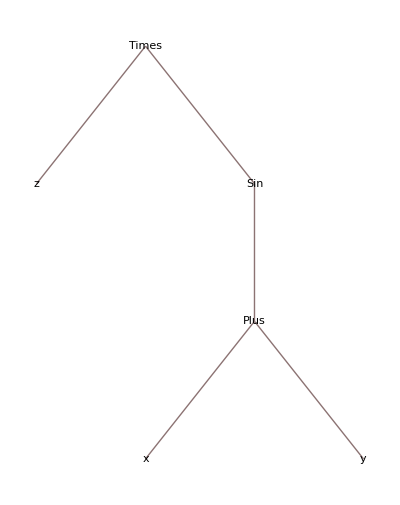

```mathematica
TreeForm[expr1]
```

### Elements of expressions

```mathematica
Head[expr1]
```

Times

```mathematica
expr2=f[g][h]
```

f[g][h]

```mathematica
FullForm[expr2]
```

f[g][h]

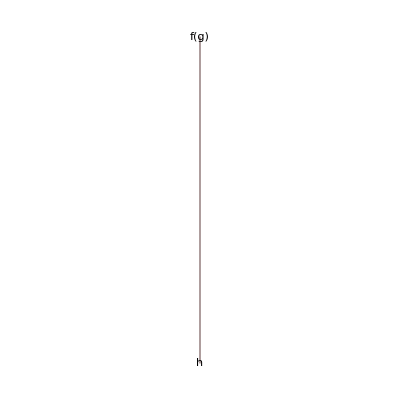

```mathematica
TreeForm[expr2]
```

```mathematica
Head[expr2]
```

f[g]

```mathematica
Head[Head[expr2]]
```

f

```mathematica
FullForm[a[[2]]]
```

Part::partd: Part specification a ⟦ 2 ⟧ is longer than depth of object.

Part[a,2]